## Run at start

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Notation

### General Notation

```mathematica
(*The file Magnus Operator contains the N-operator itself.*)
(*The file Magnus Amplitudes contains matrix elements of the N-operator.*)
(*Both the N-operator and the matrix elements are written as lists of graphs and their coefficients.*)
(*Directed edges correspond to retarded/advanced propagators iΔ^(R/A), undirected edges correspond to cuts Δ^(1)*)
(* For example, for 4 vertices at tree-level:*)
nOperator=Get["Magnus Operator\\positionSpace4V0L.m"];
nMatrix=Get["Magnus Amplitudes\\momentumSpace4V0L.m"];
```

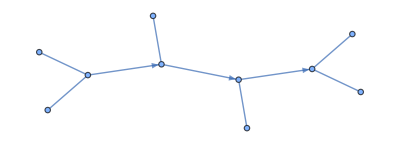
{-Graphics-,1/4}

```mathematica
nMatrix[[1]]
```

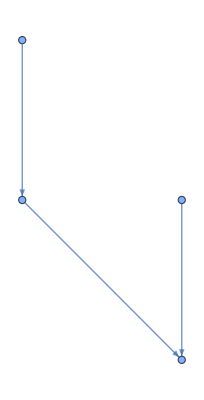
{-Graphics-,1/48}

```mathematica
nOperator[[1]]
```

### N-Operator Notation

```mathematica
(*The general expansion of the N-operator is given in (6.18) of the paper.*) 
(*The coefficients we include in these files are the ratio  (ω(τ))/(σ(τ))1/(Degree factors), where (Degree factors) are the n! type terms that appear with external vertices of a graph, see for example (6.19)*)
(*To extract the ratio (ω(τ))/(σ(τ)), we can just multiply by these (Degree factors), which are easily extracted from the Graph*)
(*For Example:*)
Clear[degreeFactor];
degreeFactor[graph_]:=Module[{degreesLeft=(3-#)&/@VertexDegree[graph]},
Times@@(Factorial/@degreesLeft)
]
```

```mathematica
(*We can compute the symmetry factor of a graph using for example:*)
Clear[generateTranspositions]
generateTranspositions[inds_,n_]:=Range[n]/.#&/@Table[{inds[[i]]->inds[[i+1]],inds[[i+1]]->inds[[i]]},{i,1,Length[inds]-1}]
generateTranspositions[{i_},n_]:={Range[n]}

Clear[graphSymmetryGroup]
graphSymmetryGroup[g_]:=Module[{n=Length@VertexList@g,perms,rules,graphPerms,syms,canEdgeList,degreeGroups},
canEdgeList=Sort@(EdgeList[g]//.{UndirectedEdge[x_,y_]:>UndirectedEdge@@Sort[{x,y}]});
degreeGroups=Pick[VertexList[g],VertexDegree[g],#]&/@Union[VertexDegree[g]];
perms=PermutationList[#,n]&/@GroupElements[
PermutationGroup[Join@@(generateTranspositions[#,n]&/@degreeGroups)]
];
rules=Inner[Rule,Range[n],#,List]&/@perms;
graphPerms=(EdgeList[g]/.#&/@rules)//.{UndirectedEdge[x_,y_]:>UndirectedEdge@@Sort[{x,y}]};
syms=And@@Inner[Equal,canEdgeList,#,List]&/@(Sort/@graphPerms);
syms=syms//.{Equal[DirectedEdge[i_,j_],DirectedEdge[k_,l_]]:>(i==k&&j==l),Equal[UndirectedEdge[i_,j_],UndirectedEdge[k_,l_]]:>Sort[{i,j}]==Sort[{k,l}]};
Pick[perms,syms]
]
```

```mathematica
(*Symmetry factors*)
VertexReplace[#,{x1->1,x2->2,x3->3,x4->4}]&/@nOperator[[All,1]];(*graphSymmetryGroup expects a graph with vertices {1,...,n}*)
Length/@graphSymmetryGroup/@%;
symFactors=%
```

{1,1,1,2,2,1}

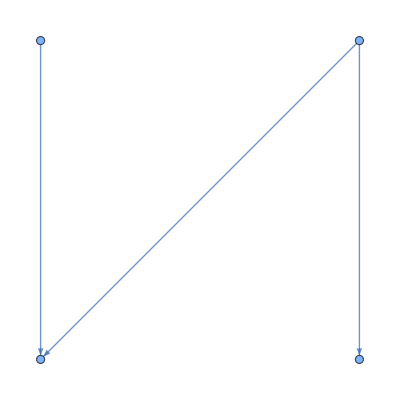
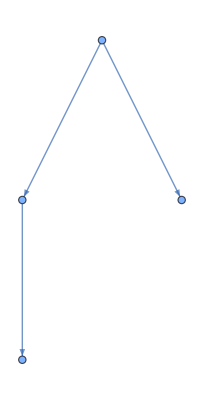
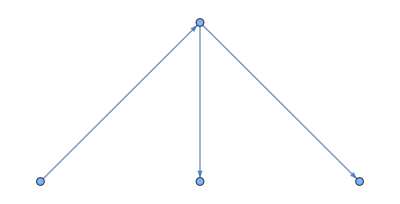
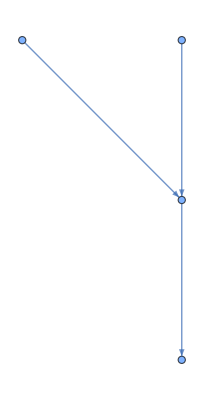
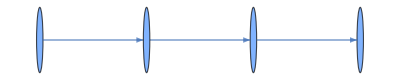
{{-Graphics-,1/12},{-Graphics-,1/12},{-Graphics-,1/12},{-Graphics-,1/6},{-Graphics-,1/6},{-Graphics-,1/4}}

```mathematica
degreeFactor/@nOperator[[All,1]];
nOperator[[All,2]]*%*symFactors;
Inner[List,nOperator[[All,1]],%,List] (*Graphs, and the Murua coefficient ω(τ)*)
```

```mathematica
(*The graphs themselves contain all the information to recover the full result for the N-operator in ϕ^3-theory. See the definition of I in (6.19).*)
```

### Matrix element Notation

```mathematica
(*The general expansion of the N-matrix elements is given in (6.20) of the paper.*) 
(*The coefficients we include in these files are the ratio  (ω(g))/(σ(g)), where now g is a graph with external legs which have been labeled ei where i runs from 1 to n.*) 
(*For example, at six points tree level:*)

nMatrix[[1]]
EdgeList[%[[1]]]
```

{-Graphics-,1/4}

{1->2,2->3,3->4,1<->e1,1<->e3,2<->e4,3<->e5,4<->e2,4<->e6}

```mathematica
(*Again, the graphs themselves contain all the information to recover the full result for the N-matrix elements in ϕ^3-theory. See the definition of J in (6.21).*)
```